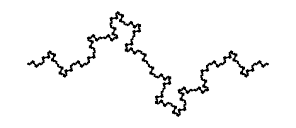

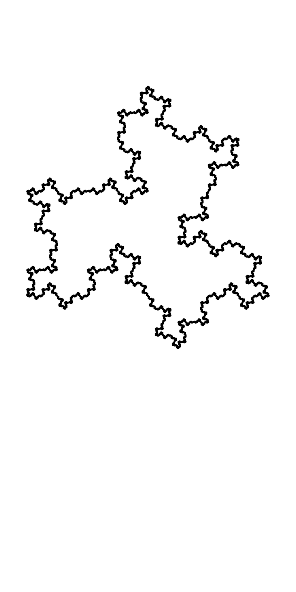

```mathematica
(*базовый сегмент фрактала*)
Segment0={{0,0},{1/4,0},{3/8,Sqrt[3]/8},{1/2,0},{5/8,-Sqrt[3]/8},{3/4,0},{1,0}};
(*матрица поворота аффинного преобразования единичного отрезка на оси абсцисс в заданный*)
Rot[{{x1_,y1_},{x2_,y2_}}]:=({{x2-x1,y1-y2},{y2-y1,x2-x1}});

Segment[{r1_,r2_}]:=With[{rot=Rot[{r1,r2}]},(*матрица поворота сегмента*)(*точки вставляемого сегмента*)With[{points=Table[rot.point+r1,{point,Segment0}]},(*преобразуем набор точек в линии сегмента*)Transpose@{Most[points],Rest[points]}]];

L[lines_]:=Join@@(Segment/@lines);

DrawCurve[basePoints_,n_,OptionsPattern[]]:=(*по точка восстановим линии исходного контура*)With[{b=Transpose@{Most[basePoints],Rest[basePoints]}},Graphics[Line[Join@@Nest[L,b,n]],PlotRange->OptionValue[PlotRange]]];
Options[DrawCurve]={PlotRange->{{0,1},{0,1}}};


(*обычный фрактал Коха*)
DrawCurve[{{0,0},{1,0}},4,PlotRange-> All]

(*снежинка Коха*)
DrawCurve[{{0,0},{0.5,Sqrt[3]/2},{1,0},{0,0}},5,PlotRange->{{0,1},{-1,1}}]
```